```mathematica
(*This reads in excel data produced from mumax3 and plots X-Y plane slices and Y-Z (wire cross section slices, can use sliders to pick slice and there are several different visualizations of the data) of the field data. Can find plots for supplementary figures here, need to run code sequentially.

The effective B field is produced in the excel sheet in  z-slices, the data is given X by Y slices with the rows the X coordinates and collums the Y coordinate. This means this you see all the z slices s of Bx, then By and then Bz. The number of x,y and z coordinates are given in the batch file (using mumax convert) which runs and processes the mumax file.

The files produced from MuMax3 will be be called B_eff or B_eff.regionN00000 depending on if you want field data for whole simualtion box or specifc region. Note that the file outputs the whole simualtion box but will give zeros if your region is outisde the simulation box or not defined somewhere in the box.

Reading in excel starts at index=1. Reading in a blank cell breaks the reading in, need to be correct size. The data stored in the excel file is fliped along the y axis compared this being plotted. I.e. data at the bottom of the z slice is actually at the top. The output from mumax3 and this flip it back when plotting
*)

(*Exporting csv files as .mx so they can be on GitHub*)
(*Export["..\\MuMax3\\Single Wire - Dragonfly\\HeatMap_InsideWire\\SingleWire_NoHysteresis_HeatMap.out\\B_eff.region41000000_fixed.mx",FieldData];*)
(*inputfile=ImportString["..\\MuMax3\\Single Wire - Dragonfly\\HeatMap_InsideWire\\SingleWire_NoHysteresis_HeatMap_aroundWire.out\\B_eff.region41000000_fixed.mx"];
FieldData=Import[inputfile];*)
```

CreateDirectory::filex: C:\Users\Frolov Labuser\Documents\MalcolmJ\MicroMagneticPaperGitHub\Mathematica\Mathematica_out\FigureS8_9-HeatMapAndInsideWireData\ already exists.

512

42

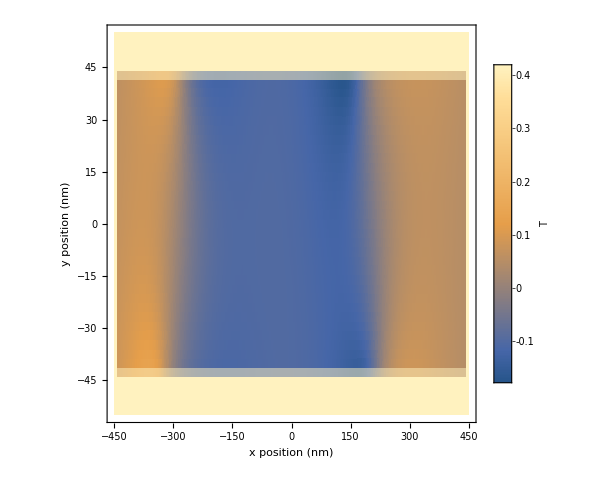

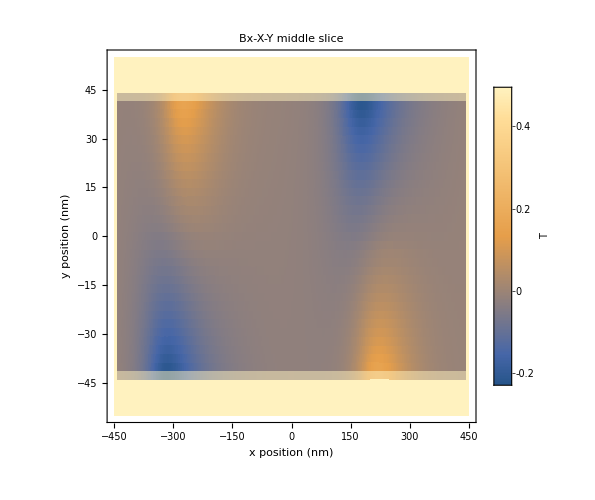

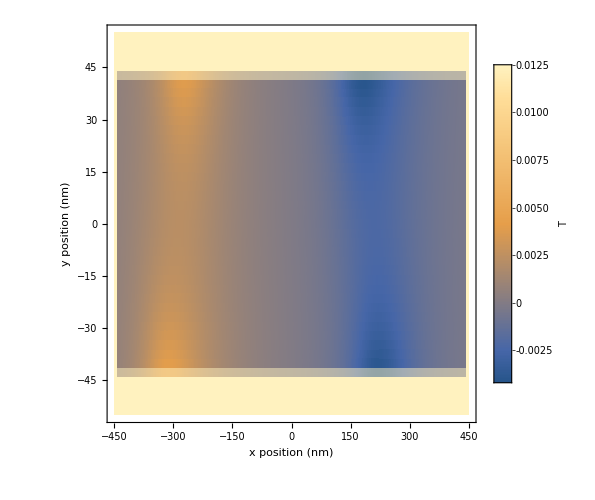

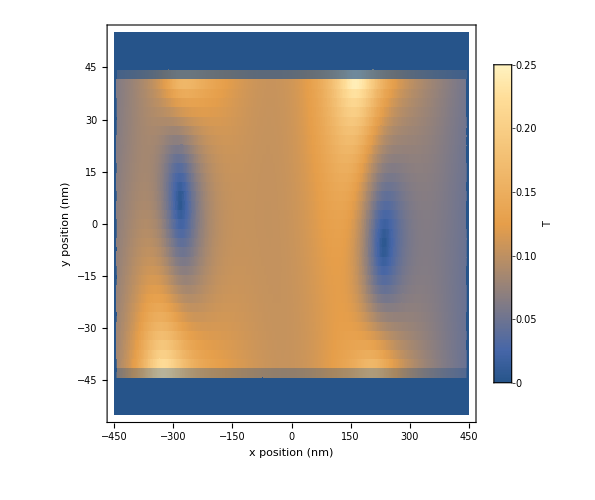

```mathematica
(*This loads in the data witb the appropiate parametrs for the given data set.This is specific to wire position etc.This section is to plot slices of Bx,By,Bz and Bmag looking down and along the X-Y plane in a shape close to the nanowire.*)

(*inputfile=ImportString["..\\MuMax3\\Single Wire - Dragonfly\\HeatMap_InsideWire\\SingleWire_NoHysteresis_HeatMap.out\\B_eff.region41000000.csv"];
FieldData=Import[inputfile,"Data"];*)

inputfile=ImportString["..\\MuMax3\\Single Wire - Dragonfly\\HeatMap_InsideWire\\SingleWire_NoHysteresis_HeatMap.out\\B_eff.region41000000_fixed.mx"];
FieldData=Import[inputfile];

(*FilePrint[inputfile]*)(*Prints out data*)
fileInfo="FigureS8_9-HeatMapAndInsideWireData";


SetDirectory[NotebookDirectory[]];
(*Setting where plots are created to current folder where this file is (or telling path to start from here)*)
CreateDirectory[StringJoin[{"Mathematica_out/",fileInfo,"/"}]];


(*Number of points for each direction,found in the batch file*)
(*Nz is the number of layers the data is given out for*)
Nx=1024;
Ny=512;
Nz=32;

zlayer=15; (*Which z layer (given in Nz) I am chosing,it is a z slice I am plotting.FIRST SLICE IS 0*) numZerosStartTopX=235; (*Number of rows of 0 that appear at the top of z-slice of data in excel.Note this is bottom of plotting range*)numZerosEndBottomX=235;(*Number of rows of 0 that appear at end of chunks of data in excel*)numZerosStartTopY=452;
numZerosStartBottomY=60;

TopRowStart=numZerosStartTopX+zlayer*Ny+zlayer+1;(*Row to start ON.Needs the 1 to start on row 1,the row end doesnt*)TopRowEnd=Ny-numZerosEndBottomX+zlayer*Ny+zlayer;

TopRowStarty=numZerosStartTopX+zlayer*Ny+zlayer+(Nz+1+Nz*Ny);
TopRowEndy=Ny-numZerosEndBottomX+zlayer*Ny+zlayer+(Nz+Nz*Ny);

TopRowStartz=numZerosStartTopX+zlayer*Ny+zlayer+2*(Nz+Nz*Ny)+1;
TopRowEndz=Ny-numZerosEndBottomX+zlayer*Ny+zlayer+2*(Nz+Nz*Ny);


Bx=FieldData[[TopRowStart;;TopRowEnd,1+numZerosStartTopY;;Nx-numZerosStartBottomY]];
By=FieldData[[TopRowStarty;;TopRowEndy,1+numZerosStartTopY;;Nx-numZerosStartBottomY]];
Bz=FieldData[[TopRowStartz;;TopRowEndz,1+numZerosStartTopY;;Nx-numZerosStartBottomY]];
BxNan=Bx/.x_/;x==0->3*Max[Bx];
(*BxNan=Bx/.x_/;x==0->0.55555555;*)
ByNan=By/.x_/;x==0->3*Max[By];
BzNan=Bz/.x_/;x==0->3*Max[Bz];
(*BxNan=Bx/.x_/;x==0->NaN;*)

Bmag=Sqrt[Bx^2+By^2+Bz^2];

ZPointaWire=Dimensions[Bx][[2]]
YPointaWire=Dimensions[Bx][[1]](*Number of data points in Y-direction for data*)



(*xDistance=heatMapData[[lengthOfData,11]]*10^9;(*Taking max of x distance covered and finding range*)yDistance=heatMapData[[lengthOfData,12]]*10^9;(*Only records y at end of regions*)*)

xDistance=900;(*Taking max of x distance covered and finding range*)yDistance=110;(*Only records y at end of regions*)BxPlot=ListDensityPlot[BxNan,DataRange->{{-xDistance/2,xDistance/2},{-yDistance/2,yDistance/2}},ClippingStyle->Blue,PlotLegends->BarLegend[Automatic,LegendLabel->"T"],PlotRange->{2.95*Min[Bx],2.95*Max[Bx]},(*PlotLabel->StringJoin[{"Bx-",PlotLabelName}],*)LabelStyle->{FontFamily->"Helvetica",20,GrayLevel[0]},ImageSize->500,Frame->True,FrameLabel->{{HoldForm["y position (nm)"],None},{HoldForm["x position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Small]]]

ByPlot=ListDensityPlot[ByNan,DataRange->{{-xDistance/2,xDistance/2},{-yDistance/2,yDistance/2}},ClippingStyle->Blue,PlotLegends->BarLegend[Automatic,LegendLabel->"T"],PlotRange->{2.9*Min[By],2.9*Max[By]},PlotLabel->StringJoin[{"Bx-","X-Y middle slice"}],LabelStyle->{FontFamily->"Helvetica",20,GrayLevel[0]},ImageSize->500,Frame->True,FrameLabel->{{HoldForm["y position (nm)"],None},{HoldForm["x position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Small]]]

BzPlot=ListDensityPlot[BzNan,DataRange->{{-xDistance/2,xDistance/2},{-yDistance/2,yDistance/2}},ClippingStyle->Blue,PlotLegends->BarLegend[Automatic,LegendLabel->"T"],PlotRange->{2.95*Min[Bz],2.95*Max[Bz]},(*PlotLabel->StringJoin[{"Bx-",PlotLabelName}],*)LabelStyle->{FontFamily->"Helvetica",20,GrayLevel[0]},ImageSize->500,Frame->True,FrameLabel->{{HoldForm["y position (nm)"],None},{HoldForm["x position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Small]]]

BmagPlot=ListDensityPlot[Bmag,DataRange->{{-xDistance/2,xDistance/2},{-yDistance/2,yDistance/2}},ClippingStyle->Blue,PlotLegends->BarLegend[Automatic,LegendLabel->"T"],PlotRange->{Min[Bmag],Max[Bmag]},(*PlotLabel->StringJoin[{"Bx-",PlotLabelName}],*)LabelStyle->{FontFamily->"Helvetica",24,GrayLevel[0]},ImageSize->500,(*Frame->True,*)FrameLabel->{{HoldForm["y position (nm)"],None},{HoldForm["x position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Small]]]


Dimensions[Bz];
Dimensions[FieldData];
```

```mathematica
(*Making 3D matrix with all Bx,By,Bz slices in the Y-Z plane.Loops over all the z-layers in the data.Not Hexagon yet*)numZerosLeft=456;
numZerosRight=62;

StartShift=85;
EndShift=110;

(*StartShift=0;
EndShift=0;*)


BxXSliceAll=Table[
BxXSlice=Table[
TopRowStart=numZerosStartTopX+zlayer*Ny+zlayer+1;
TopRowEnd=Ny-numZerosEndBottomX+zlayer*Ny+zlayer;
Bx=FieldData[[TopRowStart;;TopRowEnd,lll]],{zlayer,0,Nz-1}]
(*Print[lll]*),{lll,numZerosLeft+StartShift,Nx-numZerosRight-EndShift}];

ByXSliceAll=Table[
ByXSlice=Table[
TopRowStart=numZerosStartTopX+zlayer*Ny+zlayer+1;
TopRowEnd=Ny-numZerosEndBottomX+zlayer*Ny+zlayer;
By=FieldData[[TopRowStart;;TopRowEnd,lll]],{zlayer,Nz,2*Nz-1}]
,{lll,numZerosLeft+StartShift,Nx-numZerosRight-EndShift}];

BzXSliceAll=Table[BzXSlice=Table[TopRowStart=numZerosStartTopX+zlayer*Ny+zlayer+1;
TopRowEnd=Ny-numZerosEndBottomX+zlayer*Ny+zlayer;
Bz=FieldData[[TopRowStart;;TopRowEnd,lll]],{zlayer,2*Nz,3*Nz-1}],{lll,numZerosLeft+StartShift,Nx-numZerosRight-EndShift}];

BmagXSliceAll=Sqrt[BxXSliceAll^2+ByXSliceAll^2+BzXSliceAll^2];



Dimensions[BxXSliceAll]

sliceVal=200;

(*This takes the a single Bx slice made from above,note the end ones will probably be all zeros since I take data range a wee bit beyond wire*)
BxPlot=ListDensityPlot[BxXSliceAll[[sliceVal,All,All]],DataRange->{{-xDistance/2,xDistance/2},{-yDistance/2,yDistance/2}},ClippingStyle->Blue,PlotLegends->BarLegend[Automatic,LegendLabel->"T"],PlotRange->{2.95*Min[BxXSliceAll[[sliceVal,All,All]]],2.95*Max[BxXSliceAll[[sliceVal,All,All]]]},(*PlotLabel->StringJoin[{"Bx-",PlotLabelName}],*)LabelStyle->{FontFamily->"Helvetica",20,GrayLevel[0]},ImageSize->500,Frame->True,FrameLabel->{{HoldForm["y position (nm)"],None},{HoldForm["x position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Small]]];

ByPlot=ListDensityPlot[ByXSliceAll[[sliceVal,All,All]],DataRange->{{-xDistance/2,xDistance/2},{-yDistance/2,yDistance/2}},ClippingStyle->Blue,PlotLegends->BarLegend[Automatic,LegendLabel->"T"],PlotRange->{2.95*Min[ByXSliceAll[[sliceVal,All,All]]],2.95*Max[ByXSliceAll[[sliceVal,All,All]]]},(*PlotLabel->StringJoin[{"Bx-",PlotLabelName}],*)LabelStyle->{FontFamily->"Helvetica",20,GrayLevel[0]},ImageSize->500,Frame->True,FrameLabel->{{HoldForm["y position (nm)"],None},{HoldForm["x position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Small]]];


(*This makes a matrix where there are 5's that cut out the shape of a hexagon,add on to other matrix to draw define border of hexagon*)
HexFixMat=ConstantArray[0,{32,42}];
Do[HexFixMat[[3+2 i;;4+2 i,6;;12-i]]=5,{i,0,7}];
Do[HexFixMat[[3+2 i;;4+2 i,31+i;;37]]=5,{i,0,7}];
(*Bottom half*)
Do[HexFixMat[[29-2 i;;30-2 i,6;;12-i]]=5,{i,0,7}];
Do[HexFixMat[[29-2 i;;30-2 i,31+i;;37]]=5,{i,0,7}];
HexFixMat;
```

{312,32,42}

```mathematica
BxXSliceAllNan=BxXSliceAll/.x_/;x==0->5; (*Replacing all 0's with 5 so they appear out of range and get clipped out of figure*)

BxXSliceAllNan2=BxXSliceAllNan+Table[HexFixMat,{ooo,1,Dimensions[BxXSliceAllNan][[1]]}]; (*Adding on Hex matrix (table is copying it number tome of times to be same size as BxSlices) to make hexagon shape*)

ResizeBxXSliceAllNan=BxXSliceAllNan2[[All,All,6;;]]; (*Cutting off first few collums*)
ResizeBxXSliceAllNan2=ResizeBxXSliceAllNan[[All,All, ;;-6]];(*Cutting off last few collums*)

BxMax=Max[Flatten[BxXSliceAll]];
BxMin=Min[Flatten[BxXSliceAll]];



Manipulate[
BxPlot=ListDensityPlot[ResizeBxXSliceAllNan2[[n,1;;,1;;]],DataRange->{{-110/2,110/2},{-yDistance/2,yDistance/2}},ClippingStyle->RGBColor[120/255,120/255,120/255],PlotLegends->BarLegend[{Automatic,{BxMin,BxMax}},LegendLabel->"T"],PlotRange->{BxMin,BxMax}(*PlotRange->{2.95*Min[BxXSlice],2.95*Max[BxXSlice]}*),PlotLabel->StringJoin[{"Bx-","In Wire, Y-Z slice"}],LabelStyle->{FontFamily->"Helvetica",20,GrayLevel[0]},ImageSize->500,Frame->True,FrameLabel->{{HoldForm["z position (nm)"],None},{HoldForm["y position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Small]],ColorFunction->(ColorData["Rainbow"][Rescale[#,{BxMin,BxMax}]]&),ColorFunctionScaling->False]

,{n,1,Dimensions[BxXSliceAllNan][[1]],1,Appearance->"Labeled"}]
```

```mathematica
ByXSliceAllNan=ByXSliceAll/.x_/;x==0->5;(*Replacing all 0's with 5 so they appear out of range and get clipped out of figure*)ByXSliceAllNan2=ByXSliceAllNan+Table[HexFixMat,{ooo,1,Dimensions[ByXSliceAllNan][[1]]}];(*Adding on Hex matrix (table is copying it number tome of times to be same size as BxSlices) to make hexagon shape*)ResizeByXSliceAllNan=ByXSliceAllNan2[[All,All,6;;]];(*Cutting off first few collums*)ResizeByXSliceAllNan2=ResizeByXSliceAllNan[[All,All, ;;-6]];(*Cutting off last few collums*)

ByMax=Max[Flatten[ByXSliceAll]];
ByMin=Min[Flatten[ByXSliceAll]];

Manipulate[ByPlot=ListDensityPlot[ResizeByXSliceAllNan2[[n,1;;,1;;]],DataRange->{{-110/2,110/2},{-yDistance/2,yDistance/2}},ClippingStyle->RGBColor[120/255,120/255,120/255],PlotLegends->BarLegend[{Automatic,{ByMin,ByMax}},LegendLabel->"T"],PlotRange->{ByMin,ByMax}(*PlotRange->{2.95*Min[BxXSlice],2.95*Max[BxXSlice]}*),PlotLabel->StringJoin[{"By-","In Wire"}],LabelStyle->{FontFamily->"Helvetica",20,GrayLevel[0]},ImageSize->500,Frame->True,FrameLabel->{{HoldForm["z position (nm)"],None},{HoldForm["y position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Small]],ColorFunction->(ColorData["Rainbow"][Rescale[#,{ByMin,ByMax}]]&),ColorFunctionScaling->False],{n,1,Dimensions[ByXSliceAllNan][[1]],1,Appearance->"Labeled"}]
```

```mathematica
BzXSliceAllNan=BzXSliceAll/.x_/;x==0->5;(*Replacing all 0's with 5 so they appear out of range and get clipped out of figure*)BzXSliceAllNan2=BzXSliceAllNan+Table[HexFixMat,{ooo,1,Dimensions[BzXSliceAllNan][[1]]}];(*Adding on Hex matrix (table is copying it number tome of times to be same size as BxSlices) to make hexagon shape*)ResizeBzXSliceAllNan=BzXSliceAllNan2[[All,All,6;;]];(*Cutting off first few collums*)ResizeBzXSliceAllNan2=ResizeBzXSliceAllNan[[All,All, ;;-6]];
(*Cutting off last few collums*)

BzMax=Max[Flatten[BzXSliceAll]];
BzMin=Min[Flatten[BzXSliceAll]];

Manipulate[BzPlot=ListDensityPlot[ResizeBzXSliceAllNan2[[n,1;;,1;;]],DataRange->{{-110/2,110/2},{-yDistance/2,yDistance/2}},ClippingStyle->RGBColor[120/255,120/255,120/255],PlotLegends->BarLegend[{Automatic,{BzMin,BzMax}},LegendLabel->"T"],PlotRange->{BzMin,BzMax}(*PlotRange->{2.95*Min[BxXSlice],2.95*Max[BxXSlice]}*),PlotLabel->StringJoin[{"Bz-","In Wire"}],LabelStyle->{FontFamily->"Helvetica",20,GrayLevel[0]},ImageSize->500,Frame->True,FrameLabel->{{HoldForm["z position (nm)"],None},{HoldForm["y position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Small]],ColorFunction->(ColorData["Rainbow"][Rescale[#,{BzMin,BzMax}]]&),ColorFunctionScaling->False],
{n,1,Dimensions[BzXSliceAllNan][[1]],1,Appearance->"Labeled"}]
```

```mathematica
BmagXSliceAllNan=BmagXSliceAll/.x_/;x==0->5;(*Replacing all 0's with 5 so they appear out of range and get clipped out of figure*)BmagXSliceAllNan2=BmagXSliceAllNan+Table[HexFixMat,{ooo,1,Dimensions[BmagXSliceAllNan][[1]]}];(*Adding on Hex matrix (table is copying it number tome of times to be same size as BxSlices) to make hexagon shape*)ResizeBmagXSliceAllNan=BmagXSliceAllNan2[[All,All,6;;]];(*Cutting off first few collums*)ResizeBmagXSliceAllNan2=ResizeBmagXSliceAllNan[[All,All, ;;-6]];
(*Cutting off last few collums*)

BmagMax=Max[Flatten[BmagXSliceAll]];
BmagMin=Min[Flatten[BmagXSliceAll]];

Manipulate[BmagPlot=ListDensityPlot[ResizeBmagXSliceAllNan2[[n,1;;,1;;]],DataRange->{{-110/2,110/2},{-yDistance/2,yDistance/2}},ClippingStyle->RGBColor[120/255,120/255,120/255],PlotLegends->BarLegend[{Automatic,{BmagMin,BmagMax}},LegendLabel->"T"],PlotRange->{BmagMin,BmagMax}(*PlotRange->{2.95*Min[BxXSlice],2.95*Max[BxXSlice]}*),PlotLabel->StringJoin[{"Bmag-","In Wire"}],LabelStyle->{FontFamily->"Helvetica",20,GrayLevel[0]},ImageSize->500,Frame->True,FrameLabel->{{HoldForm["z position (nm)"],None},{HoldForm["y position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Small]],ColorFunction->(ColorData["Rainbow"][Rescale[#,{BmagMin,BmagMax}]]&),ColorFunctionScaling->False

],{n,1,Dimensions[BmagXSliceAllNan][[1]],1,Appearance->"Labeled"}]
```

Part::partd: Part specification ResizeBmagXSliceAllNan2⟦1,1;;All,1;;All⟧ is longer than depth of object.

ListDensityPlot::prng: Value of option PlotRange -> {BmagMin,BmagMax} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListDensityPlot::arrayerr: ResizeBmagXSliceAllNan2⟦1,1;;All,1;;All⟧ must be a valid array.

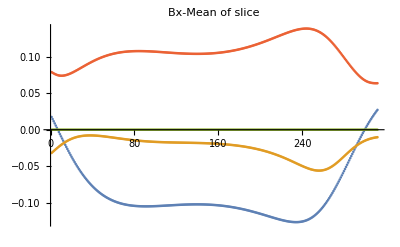

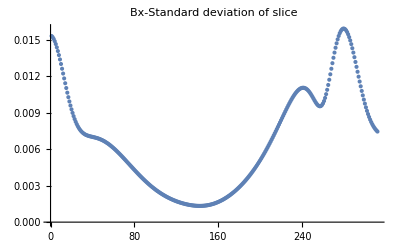

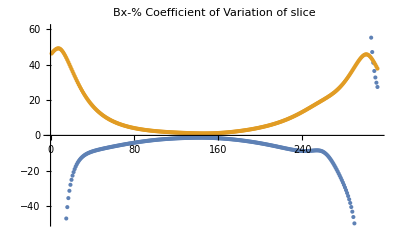

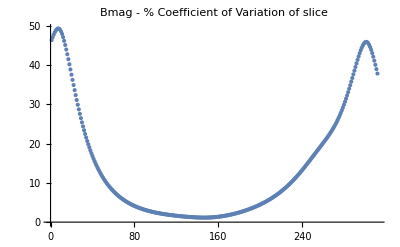

```mathematica
(*Finding average of each slice. Need to take out all points outisde the wire, all these values should be larger than 3 so they are set to nothing and then averaging is perfromed
The standard deviation is performed in a simialr way, this second data point.*)
BxAverage=Table[
SingleBxXSlice=ResizeBxXSliceAllNan2[[lll,1;;,1;;]];
{Mean[Flatten[SingleBxXSlice/.x_/;x≥3->Nothing]],StandardDeviation[Flatten[SingleBxXSlice/.x_/;x≥3->Nothing]]},{lll,1,Dimensions[ResizeBxXSliceAllNan2][[1]]}];

ByAverage=Table[SingleByXSlice=ResizeByXSliceAllNan2[[lll,1;;,1;;]];
{Mean[Flatten[SingleByXSlice/.x_/;x≥3->Nothing]],StandardDeviation[Flatten[SingleByXSlice/.x_/;x≥3->Nothing]]},{lll,1,Dimensions[ResizeByXSliceAllNan2][[1]]}];

BzAverage=Table[SingleBzXSlice=ResizeBzXSliceAllNan2[[lll,1;;,1;;]];
{Mean[Flatten[SingleBzXSlice/.x_/;x≥3->Nothing]],StandardDeviation[Flatten[SingleBzXSlice/.x_/;x≥3->Nothing]]},{lll,1,Dimensions[ResizeBzXSliceAllNan2][[1]]}];

BmagAverage=Table[
SingleBmagXSlice=ResizeBmagXSliceAllNan2[[lll,1;;,1;;]];
{meanVal=Mean[Flatten[SingleBmagXSlice/.x_/;x≥3->Nothing]],StandardDeviation[Flatten[SingleBmagXSlice/.x_/;x≥3->Nothing]],
(Max[Flatten[SingleBmagXSlice/.x_/;x≥3->Nothing]]-meanVal)},
{lll,1,Dimensions[ResizeBmagXSliceAllNan2][[1]]}];


ListPlot[{BxAverage[[All,1]],ByAverage[[All,1]],BzAverage[[All,1]],BmagAverage[[All,1]]},PlotLabel->StringJoin[{"Bx-","Mean of slice"}]]
ListPlot[BxAverage[[All,2]],PlotLabel->StringJoin[{"Bx-","Standard deviation of slice"}]]
ListPlot[{100*BxAverage[[All,2]]/BxAverage[[All,1]],100*BmagAverage[[All,2]]/BmagAverage[[All,1]]},PlotLabel->StringJoin[{"Bx-","% Coefficient of Variation of slice"}]]

ListPlot[{100*BmagAverage[[All,2]]/BmagAverage[[All,1]]},PlotLabel->StringJoin[{"Bmag - ","% Coefficient of Variation of slice"}]]
```

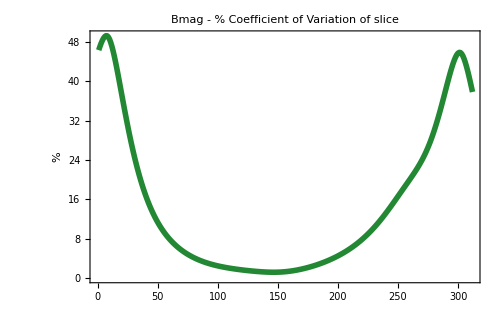

```mathematica
Colour1Plot=RGBColor[0/255,119/255,187/255];(*Blue*)Colour5Plot=RGBColor[34/255,136/255,51/255];(*Green*)textSize1=24;
frameThickness=1;

ListPlot[(100*BmagAverage[[All,2]]/BmagAverage[[All,1]]),Joined->True,InterpolationOrder->1,Frame->True,LabelStyle->{FontFamily->"Helvetica",textSize1,GrayLevel[0],Black},(*PlotLegends->Placed[{"By Profile"},{postionx1,postiony1}],*)PlotStyle->{Colour5Plot,Thickness[0.008]},FrameLabel->(*"Angle from negative x-axis"*)"%",FrameStyle->Directive[Black,AbsoluteThickness[frameThickness]],
PlotLabel->StringJoin[{"Bmag - ","% Coefficient of Variation of slice"}],
ImageSize->500
(*FrameTicksStyle->{Blue,Colour7Plot,Red,Red},*)(*PlotStyle->{Blue,Directive[Green,Dashed]},*)(*PlotRange->{Automatic,{0,negAnngle*180}},PlotRangePadding->{{0,0},{0,0}},FrameTicks->{{{0,negAnngle*30,negAnngle*60,negAnngle*90,negAnngle*120,negAnngle*150,negAnngle*180},Automatic},{filledTickPosXTop2,emptyTickPosXTop2}}*)
]
```

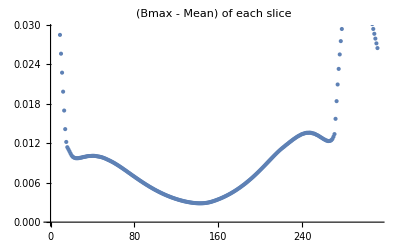

```mathematica
BxAverage2=Table[SingleBxXSlice=ResizeBxXSliceAllNan2[[lll,1;;,1;;]];
{meanVal=Mean[Flatten[SingleBxXSlice/.x_/;x≥3->Nothing]],StandardDeviation[Flatten[SingleBxXSlice/.x_/;x≥3->Nothing]],
(Max[Flatten[SingleBxXSlice/.x_/;x≥3->Nothing]]-meanVal)
},{lll,1,Dimensions[ResizeBxXSliceAllNan2][[1]]}];

ListPlot[{BxAverage2[[All,3]]},PlotLabel->StringJoin[{"(Bmax - Mean)"," of each slice"}]]
```

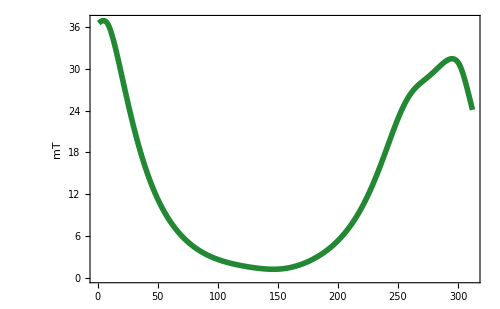

```mathematica
topNumPoints=Length[BmagAverage[[All,3]]];
totalNumPlotPointsX=700;
(*Points for length of wire*)emptyTickPosXTop2=Table[{i,""},{i,1,topNumPoints,(topNumPoints-1)/20}];
filledTickPosXTop2=emptyTickPosXTop2/.{List[1,""]->{1,StringJoin[{"    ",ToString[-totalNumPlotPointsX/2]}]},List[(topNumPoints+1)/2,""]->{(topNumPoints+1)/2,"0"},List[topNumPoints,""]->{topNumPoints,StringJoin[{ToString[totalNumPlotPointsX/2],"      "}]}};

BmagAverage=Table[
SingleBmagXSlice=ResizeBmagXSliceAllNan2[[lll,1;;,1;;]];
{meanVal=Mean[Flatten[SingleBmagXSlice/.x_/;x≥3->Nothing]],StandardDeviation[Flatten[SingleBmagXSlice/.x_/;x≥3->Nothing]],
(Max[Flatten[SingleBmagXSlice/.x_/;x≥3->Nothing]]-meanVal),
Min[Flatten[SingleBmagXSlice/.x_/;x≥3->Nothing]]},
{lll,1,Dimensions[ResizeBmagXSliceAllNan2][[1]]}];

(*BmagmaxMeanDiff*)
BmagSD=ListPlot[1000*BmagAverage[[All,2]],Joined->True,InterpolationOrder->1,Frame->True,LabelStyle->{FontFamily->"Helvetica",textSize1,GrayLevel[0],Black},(*PlotLegends->Placed[{"By Profile"},{postionx1,postiony1}],*)PlotStyle->{Colour5Plot,Thickness[0.008]},FrameLabel->(*"Angle from negative x-axis"*)"mT",FrameStyle->Directive[Black,AbsoluteThickness[frameThickness]],(*PlotLabel->StringJoin[{"(Bmax - Mean)"," of each slice"}],*)ImageSize->500,
PlotRange->All
(*FrameTicksStyle->{Blue,Colour7Plot,Red,Red},*)(*PlotStyle->{Blue,Directive[Green,Dashed]},*)(*PlotRange->{Automatic,{0,negAnngle*180}},PlotRangePadding->{{0,0},{0,0}},*)(*FrameTicks->{{Automatic,Automatic},{filledTickPosXTop2,emptyTickPosXTop2}}*)]

ListPlot[{1000*BxAverage[[All,1]],1000*ByAverage[[All,1]],1000*BzAverage[[All,1]],1000*BmagAverage[[All,1]]},PlotLabel->StringJoin[{"Bx-","Mean of slice"}]];

(*Export[StringJoin[{"Mathematica_out/",fileInfo,"/",fileInfo,"BmagSD.eps"}],BmagSD,"eps"];*)
```

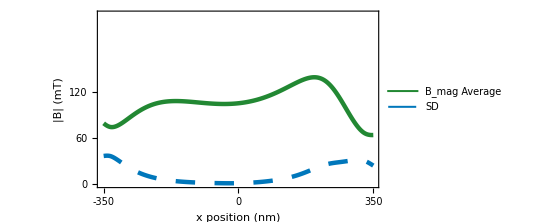

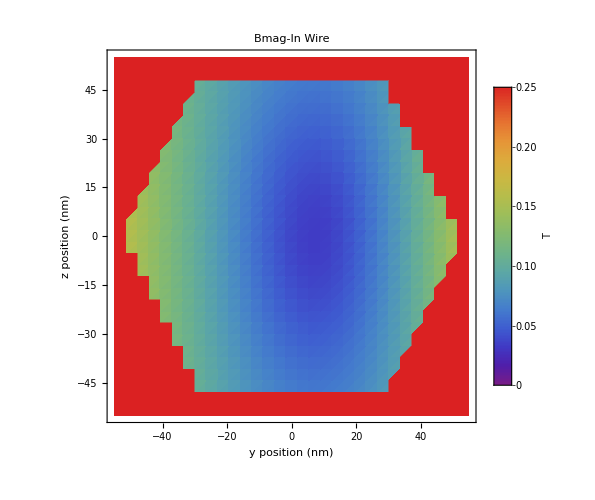

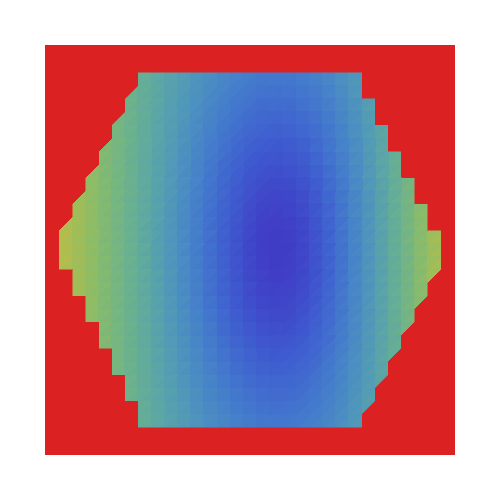

```mathematica
(*Standard deviation plot*)
BmagSD=ListPlot[{1000*BmagAverage[[All,1]],1000*BmagAverage[[All,2]]},Joined->True,InterpolationOrder->1,Frame->True,LabelStyle->{FontFamily->"Helvetica",textSize1,GrayLevel[0],Black},(*PlotLegends->Placed[{"By Profile"},{postionx1,postiony1}],*)PlotStyle->{{Colour5Plot,Thickness[0.008]},{Colour1Plot,Thickness[0.008],Dashing[Large]}},FrameLabel->{{HoldForm[(*"Magnitude of Field (mT)"*)"|B| (mT)"],None},{HoldForm["x position (nm)"],None}},FrameStyle->Directive[Black,AbsoluteThickness[frameThickness]],PlotRange->{Automatic,{0,220}},ImageSize->{800},AspectRatio->1/1.8,PlotRange->All,FrameTicks->{{Table[rrr,{rrr,0,150,30}],Automatic},{filledTickPosXTop2,emptyTickPosXTop2}},
PlotLegends->Placed[LineLegend[{"B_mag Average","SD"},LabelStyle->24],{0.5,0.25}(*,{0.9,0.88}*)]
(*FrameTicksStyle->{Blue,Colour7Plot,Red,Red},*)(*PlotStyle->{Blue,Directive[Green,Dashed]},*)(*PlotRange->{Automatic,{0,negAnngle*180}},PlotRangePadding->{{0,0},{0,0}},*)]

Export[StringJoin[{"Mathematica_out/",fileInfo,"/",fileInfo,"BmagSD.eps"}],BmagSD,"eps"];


BmagSlicePlot=ListDensityPlot[ResizeBmagXSliceAllNan2[[20,1;;,1;;]],DataRange->{{-110/2,110/2},{-110/2,110/2}},(*ClippingStyle->RGBColor[120/255,120/255,120/255]*)ClippingStyle->RGBColor[255/255,255/255,255/255],PlotLegends->BarLegend[{Automatic,{BmagMin,BmagMax}},LegendLabel->"T"],PlotRange->{BmagMin,BmagMax}(*PlotRange->{2.95*Min[BxXSlice],2.95*Max[BxXSlice]}*),PlotLabel->StringJoin[{"Bmag-","In Wire"}],LabelStyle->{FontFamily->"Helvetica",20,GrayLevel[0]},ImageSize->500,Frame->True,FrameLabel->{{HoldForm["z position (nm)"],None},{HoldForm["y position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Small]],ColorFunction->(ColorData["Rainbow"][Rescale[#,{BmagMin,BmagMax}]]&),ColorFunctionScaling->False]

ListDensityPlot[ResizeBmagXSliceAllNan2[[20,1;;,1;;]],DataRange->{{-110/2,110/2},{-110/2,110/2}},(*ClippingStyle->RGBColor[120/255,120/255,120/255]*)ClippingStyle->RGBColor[255/255,255/255,255/255],PlotRange->{BmagMin,BmagMax}(*PlotRange->{2.95*Min[BxXSlice],2.95*Max[BxXSlice]}*),LabelStyle->{FontFamily->"Helvetica",20,GrayLevel[0]},ImageSize->500,Frame->False,ColorFunction->(ColorData["Rainbow"][Rescale[#,{BmagMin,BmagMax}]]&),ColorFunctionScaling->False]


Export[StringJoin[{"Mathematica_out/",fileInfo,"/",fileInfo,"BmagSlicePlot.eps"}],BmagSlicePlot,"eps"];
```

```mathematica
sliceVals={20,90,150}
sliceVals[[1]]
Length[BmagAverage[[All,1]]]
```

{20,90,150}

20

312

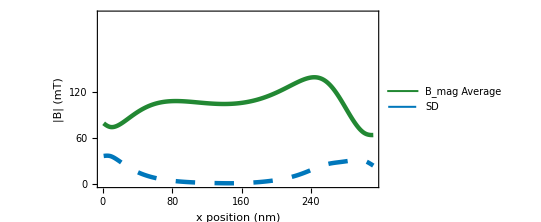

{20,90,155,250}

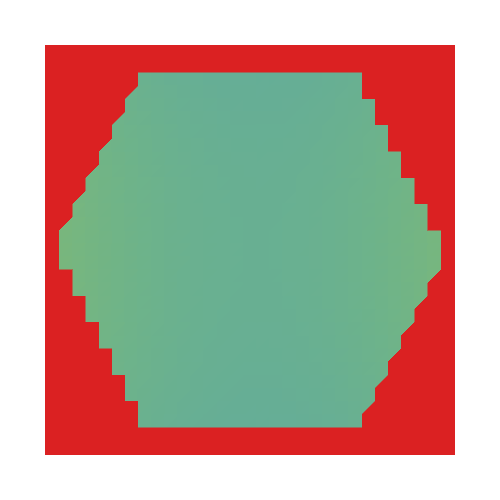
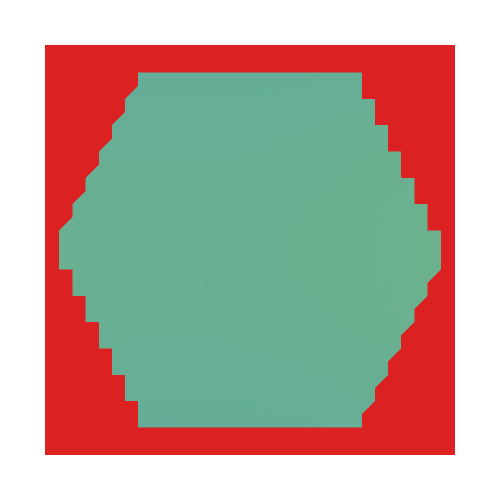
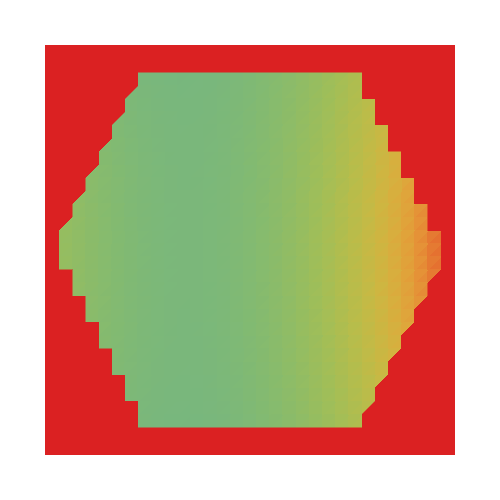
{{-Graphics-,Null},{-Graphics-,Null},{-Graphics-,Null},{-Graphics-,Null}}

```mathematica
BmagSD=ListPlot[{1000*BmagAverage[[All,1]],1000*BmagAverage[[All,2]]},Joined->True,InterpolationOrder->1,Frame->True,LabelStyle->{FontFamily->"Helvetica",textSize1,GrayLevel[0],Black},(*PlotLegends->Placed[{"By Profile"},{postionx1,postiony1}],*)PlotStyle->{{Colour5Plot,Thickness[0.008]},{Colour1Plot,Thickness[0.008],Dashing[Large]}},FrameLabel->{{HoldForm[(*"Magnitude of Field (mT)"*)"|B| (mT)"],None},{HoldForm["x position (nm)"],None}},FrameStyle->Directive[Black,AbsoluteThickness[frameThickness]],PlotRange->{Automatic,{0,220}},ImageSize->{800},AspectRatio->1/1.8,PlotRange->All,FrameTicks->{{Table[rrr,{rrr,0,150,30}],Automatic},{Table[rrr,{rrr,0,Length[BmagAverage[[All,1]]],20}],emptyTickPosXTop2}},PlotLegends->Placed[LineLegend[{"\!\(\*SubscriptBox[\(B\), \(mag\)]\) Average","SD"},LabelStyle->24],{0.5,0.25}(*,{0.9,0.88}*)]
(*FrameTicksStyle->{Blue,Colour7Plot,Red,Red},*)(*PlotStyle->{Blue,Directive[Green,Dashed]},*)(*PlotRange->{Automatic,{0,negAnngle*180}},PlotRangePadding->{{0,0},{0,0}},*)]

sliceVals={20,90,155,250}
Table[
{BmagSlice=ListDensityPlot[ResizeBmagXSliceAllNan2[[sliceVals[[mmm]],1;;,1;;]],DataRange->{{-110/2,110/2},{-110/2,110/2}},(*ClippingStyle->RGBColor[120/255,120/255,120/255]*)ClippingStyle->RGBColor[255/255,255/255,255/255],PlotRange->{BmagMin,BmagMax}(*PlotRange->{2.95*Min[BxXSlice],2.95*Max[BxXSlice]}*),LabelStyle->{FontFamily->"Helvetica",20,GrayLevel[0]},ImageSize->500,Frame->False,ColorFunction->(ColorData["Rainbow"][Rescale[#,{BmagMin,BmagMax}]]&),ColorFunctionScaling->False],

Export[StringJoin[{"Mathematica_out/",fileInfo,"/",fileInfo,"BmagSlice",ToString[sliceVals[[mmm]]],".eps"}],BmagSlice,"eps"];},

{mmm,1,4}]
```

```mathematica
BxAveDiffAllSlices=Table[
AveMatrix=BxAverage[[ppp,1]]*ConstantArray[1,{Dimensions[ResizeBxXSliceAllNan2][[2]],Dimensions[ResizeBxXSliceAllNan2][[3]]}]; (*Making a matrix size of Bx slice with all BxAve values to subtarct*)
Abs[100*(ResizeBxXSliceAllNan2[[ppp,1;;,1;;]]-AveMatrix)/BxAverage[[ppp,1]]],
(*Take abs % value of difference between average value and BxSlice*)
{ppp,1,Dimensions[ResizeBxXSliceAllNan2][[1]]}];


Manipulate[Overlay[{ListDensityPlot[BxAveDiffAllSlices[[n,1;;,1;;]],DataRange->{{-100/2,100/2},{-yDistance/2,yDistance/2}},ClippingStyle->RGBColor[120/255,120/255,120/255],PlotLegends->BarLegend[{Automatic,{0,100}},LegendLabel->"%"],PlotRange->{0,100}(*PlotRange->{2.95*Min[BxXSlice],2.95*Max[BxXSlice]}*),PlotLabel->StringJoin[{"Bx-","Percentage difference of ave of slice"}],LabelStyle->{FontFamily->"Helvetica",20,GrayLevel[0]},ImageSize->500,Frame->True,FrameLabel->{{HoldForm["z position (nm)"],None},{HoldForm["y position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Small]],ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,100}]]&),ColorFunctionScaling->False

],ToString[Style[BxAverage[[n,1]],White],StandardForm]},Alignment->{0.55,0.78}],{n,1,Dimensions[ResizeBxXSliceAllNan2][[1]],1,Appearance->"Labeled"}]
```

Part::partd: Part specification BxAveDiffAllSlices⟦1,1;;All,1;;All⟧ is longer than depth of object.

ListDensityPlot::arrayerr: BxAveDiffAllSlices⟦1,1;;All,1;;All⟧ must be a valid array.

Part::partd: Part specification BxAverage⟦1,1⟧ is longer than depth of object.

```mathematica
(*Export["SingleWire_NoHysteresis_HeatMap_aroundWire.csv",FieldData]
FieldData=Import[inputfile,"SingleWire_NoHysteresis_HeatMap_aroundWire.dat"];*)

(*Export["..\\MuMax3\\Single Wire - Dragonfly\\HeatMap_InsideWire\\SingleWire_NoHysteresis_HeatMap_aroundWire.out\\B_eff.region41000000_fixed.mx",FieldData];
inputfile=*)ImportString["..\\MuMax3\\Single Wire - Dragonfly\\HeatMap_InsideWire\\SingleWire_NoHysteresis_HeatMap_aroundWire.out\\B_eff.region41000000_fixed.mx"];
FieldData=Import[inputfile,"Data"];




(*(*Exporting wavefunction data to be used in T-Junction colour plot*)Export[StringJoin[{"Mathematica_out/",fileInfo,"/",fileInfo,"ψlevel",ToString[gateStrengths[[1]]/100000],ToString[gateStrengths[[2]]/100000],ToString[gateStrengths[[3]]/100000],".xls"}],ψlevel]

Export[StringJoin[{"Mathematica_out/",fileInfo,"/",fileInfo,"ψlevelLeg",ToString[gateStrengths[[1]]/100000],ToString[gateStrengths[[2]]/100000],ToString[gateStrengths[[3]]/100000],".xls"}],ψlevelLeg]*)
```

Import::noelem: The Import element "Data" is not present when importing as MX.

```mathematica
FieldData
```

$Failed

```mathematica
(*This loads in the data witb the appropiate parametrs for the given data set.This is specific to wire position etc.This section is to plot slices of Bx,By,Bz and Bmag looking down and along the X-Y plane in a shape close to the nanowire.*)
inputfile=ImportString["..\\MuMax3\\Single Wire - Dragonfly\\HeatMap_InsideWire\\SingleWire_NoHysteresis_HeatMap_aroundWire.out\\B_eff.region41000000.csv"];
FieldData=Import[inputfile,"Data"];

(*inputfile=ImportString["..\\MuMax3\\Single Wire - Dragonfly\\HeatMap_InsideWire\\SingleWire_NoHysteresis_HeatMap_aroundWire.out\\B_eff.region41000000_fixed.csv"];*)

(*FilePrint[inputfile]*)(*Prints out data*)
fileInfo="FigureS8_9-HeatMapAndInsideWireData";

SetDirectory[NotebookDirectory[]];
(*Setting where plots are created to current folder where this file is (or telling path to start from here)*)
CreateDirectory[StringJoin[{"Mathematica_out/",fileInfo,"/"}]];


(*Number of points for each direction,found in the batch file*)
(*Nz is the number of layers the data is given out for*)
Nx=1024;
Ny=512;
Nz=32;

zlayer=15;(*Which z layer (given in Nz) I am chosing,it is a z slice I am plotting.FIRST SLICE IS 0*)numZerosStartTopX=200;(*Number of rows of 0 that appear at the top of z-slice of data in excel.Note this is bottom of plotting range*)numZerosEndBottomX=200;(*Number of rows of 0 that appear at end of chunks of data in excel*)numZerosStartTopY=680;
numZerosStartBottomY=120;

TopRowStart=numZerosStartTopX+zlayer*Ny+zlayer+1;(*Row to start ON.Needs the 1 to start on row 1,the row end doesnt*)TopRowEnd=Ny-numZerosEndBottomX+zlayer*Ny+zlayer;

TopRowStarty=numZerosStartTopX+zlayer*Ny+zlayer+(Nz+1+Nz*Ny);
TopRowEndy=Ny-numZerosEndBottomX+zlayer*Ny+zlayer+(Nz+Nz*Ny);

TopRowStartz=numZerosStartTopX+zlayer*Ny+zlayer+2*(Nz+Nz*Ny)+1;
TopRowEndz=Ny-numZerosEndBottomX+zlayer*Ny+zlayer+2*(Nz+Nz*Ny);


Bx=FieldData[[TopRowStart;;TopRowEnd,1+numZerosStartTopY;;Nx-numZerosStartBottomY]];
By=FieldData[[TopRowStarty;;TopRowEndy,1+numZerosStartTopY;;Nx-numZerosStartBottomY]];
Bz=FieldData[[TopRowStartz;;TopRowEndz,1+numZerosStartTopY;;Nx-numZerosStartBottomY]];
BxNan=Bx/.x_/;x==0->3*Max[Bx];
(*BxNan=Bx/.x_/;x==0->0.55555555;*)
ByNan=By/.x_/;x==0->3*Max[By];
BzNan=Bz/.x_/;x==0->3*Max[Bz];
(*BxNan=Bx/.x_/;x==0->NaN;*)

Bmag=Sqrt[Bx^2+By^2+Bz^2];

ZPointaWire=Dimensions[Bx][[2]]
YPointaWire=Dimensions[Bx][[1]](*Number of data points in Y-direction for data*)



(*xDistance=heatMapData[[lengthOfData,11]]*10^9;(*Taking max of x distance covered and finding range*)yDistance=heatMapData[[lengthOfData,12]]*10^9;(*Only records y at end of regions*)*)

xDistance=400;(*Taking max of x distance covered and finding range*)yDistance=400;(*Only records y at end of regions*)BxPlot=ListDensityPlot[BxNan,DataRange->{{-xDistance/2,xDistance/2},{-yDistance/2,yDistance/2}},ClippingStyle->Blue,PlotLegends->BarLegend[Automatic,LegendLabel->"T"],PlotRange->{2.95*Min[Bx],2.95*Max[Bx]},(*PlotLabel->StringJoin[{"Bx-",PlotLabelName}],*)LabelStyle->{FontFamily->"Helvetica",20,GrayLevel[0]},ImageSize->500,Frame->True,FrameLabel->{{HoldForm["y position (nm)"],None},{HoldForm["x position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Small]]]

ByPlot=ListDensityPlot[ByNan,DataRange->{{-xDistance/2,xDistance/2},{-yDistance/2,yDistance/2}},ClippingStyle->Blue,PlotLegends->BarLegend[Automatic,LegendLabel->"T"],PlotRange->{2.9*Min[By],2.9*Max[By]},(*PlotLabel->StringJoin[{"Bx-",PlotLabelName}],*)LabelStyle->{FontFamily->"Helvetica",20,GrayLevel[0]},ImageSize->500,Frame->True,FrameLabel->{{HoldForm["y position (nm)"],None},{HoldForm["x position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Small]]]

BzPlot=ListDensityPlot[BzNan,DataRange->{{-xDistance/2,xDistance/2},{-yDistance/2,yDistance/2}},ClippingStyle->Blue,PlotLegends->BarLegend[Automatic,LegendLabel->"T"],PlotRange->{2.95*Min[Bz],2.95*Max[Bz]},(*PlotLabel->StringJoin[{"Bx-",PlotLabelName}],*)LabelStyle->{FontFamily->"Helvetica",20,GrayLevel[0]},ImageSize->500,Frame->True,FrameLabel->{{HoldForm["y position (nm)"],None},{HoldForm["x position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Small]]]


BmagPlot=ListDensityPlot[Bmag,DataRange->{{-xDistance/2,xDistance/2},{-yDistance/2,yDistance/2}},ClippingStyle->Blue,PlotLegends->BarLegend[Automatic,LegendLabel->"T"],PlotRange->{Min[Bmag],Max[Bmag]},(*PlotLabel->StringJoin[{"Bx-",PlotLabelName}],*)LabelStyle->{FontFamily->"Helvetica",24,GrayLevel[0]},ImageSize->500,(*Frame->True,*)FrameLabel->{{HoldForm["y position (nm)"],None},{HoldForm["x position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Small]],
ColorFunction->(ColorData["SunsetColors"][Rescale[#,{Min[Bmag],Max[Bmag]}]]&),ColorFunctionScaling->False]


Dimensions[Bz];
Dimensions[FieldData];
```

CreateDirectory::filex: C:\Users\Frolov Labuser\Documents\MalcolmJ\MicroMagneticPaperGitHub\Mathematica\Mathematica_out\FigureS8_9-HeatMapAndInsideWireData\ already exists.

Part::take: Cannot take positions 7896 through 8007 in $Failed.

Part::take: Cannot take positions 24312 through 24423 in $Failed.

Part::take: Cannot take positions 40728 through 40839 in $Failed.

Part::partw: Part 2 of {3} does not exist.

{3}⟦2⟧

3

ListDensityPlot::prng: Value of option PlotRange -> {2.95 $Failed⟦7896;;8007,681;;904⟧,2.95 $Failed⟦7896;;8007,681;;904⟧} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListDensityPlot::arrayerr: $Failed⟦7896;;8007,681;;904⟧ must be a valid array.

ListDensityPlot[$Failed⟦7896;;8007,681;;904⟧,DataRange→{{-200,200},{-200,200}},ClippingStyle→RGBColor[0, 0, 1],PlotLegends→BarLegend[Automatic,LegendLabel→T],PlotRange→{2.95 $Failed⟦7896;;8007,681;;904⟧,2.95 $Failed⟦7896;;8007,681;;904⟧},LabelStyle→{FontFamily→Helvetica,20,GrayLevel[0]},ImageSize→500,Frame→True,FrameLabel→{{y position (nm),None},{x position (nm),None}},FrameStyle→Directive[GrayLevel[0],Thickness[Small]]]

ListDensityPlot::prng: Value of option PlotRange -> {2.9 $Failed⟦24312;;24423,681;;904⟧,2.9 $Failed⟦24312;;24423,681;;904⟧} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListDensityPlot::arrayerr: $Failed⟦24312;;24423,681;;904⟧ must be a valid array.

ListDensityPlot[$Failed⟦24312;;24423,681;;904⟧,DataRange→{{-200,200},{-200,200}},ClippingStyle→RGBColor[0, 0, 1],PlotLegends→BarLegend[Automatic,LegendLabel→T],PlotRange→{2.9 $Failed⟦24312;;24423,681;;904⟧,2.9 $Failed⟦24312;;24423,681;;904⟧},LabelStyle→{FontFamily→Helvetica,20,GrayLevel[0]},ImageSize→500,Frame→True,FrameLabel→{{y position (nm),None},{x position (nm),None}},FrameStyle→Directive[GrayLevel[0],Thickness[Small]]]

ListDensityPlot::prng: Value of option PlotRange -> {2.95 $Failed⟦40728;;40839,681;;904⟧,2.95 $Failed⟦40728;;40839,681;;904⟧} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListDensityPlot::arrayerr: $Failed⟦40728;;40839,681;;904⟧ must be a valid array.

ListDensityPlot[$Failed⟦40728;;40839,681;;904⟧,DataRange→{{-200,200},{-200,200}},ClippingStyle→RGBColor[0, 0, 1],PlotLegends→BarLegend[Automatic,LegendLabel→T],PlotRange→{2.95 $Failed⟦40728;;40839,681;;904⟧,2.95 $Failed⟦40728;;40839,681;;904⟧},LabelStyle→{FontFamily→Helvetica,20,GrayLevel[0]},ImageSize→500,Frame→True,FrameLabel→{{y position (nm),None},{x position (nm),None}},FrameStyle→Directive[GrayLevel[0],Thickness[Small]]]

ListDensityPlot::prng: Value of option PlotRange -> {√(($Failed⟦7896;;8007,681;;904⟧)^2+($Failed⟦24312;;24423,681;;904⟧)^2+($Failed⟦40728;;40839,681;;904⟧)^2),√(($Failed⟦7896;;8007,681;;904⟧)^2+($Failed⟦24312;;24423,681;;904⟧)^2+($Failed⟦40728;;40839,681;;904⟧)^2)} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListDensityPlot::arrayerr: √(($Failed⟦7896;;8007,681;;904⟧)^2+($Failed⟦24312;;24423,681;;904⟧)^2+($Failed⟦40728;;40839,681;;904⟧)^2) must be a valid array.

ListDensityPlot[√(($Failed⟦7896;;8007,681;;904⟧)^2+($Failed⟦24312;;24423,681;;904⟧)^2+($Failed⟦40728;;40839,681;;904⟧)^2),DataRange→{{-200,200},{-200,200}},ClippingStyle→RGBColor[0, 0, 1],PlotLegends→BarLegend[Automatic,LegendLabel→T],PlotRange→{√(($Failed⟦7896;;8007,681;;904⟧)^2+($Failed⟦24312;;24423,681;;904⟧)^2+($Failed⟦40728;;40839,681;;904⟧)^2),√(($Failed⟦7896;;8007,681;;904⟧)^2+($Failed⟦24312;;24423,681;;904⟧)^2+($Failed⟦40728;;40839,681;;904⟧)^2)},LabelStyle→{FontFamily→Helvetica,24,GrayLevel[0]},ImageSize→500,FrameLabel→{{y position (nm),None},{x position (nm),None}},FrameStyle→Directive[GrayLevel[0],Thickness[Small]],ColorFunction→(ColorData[SunsetColors][Rescale[#1,{Min[Bmag],Max[Bmag]}]]&),ColorFunctionScaling→False]

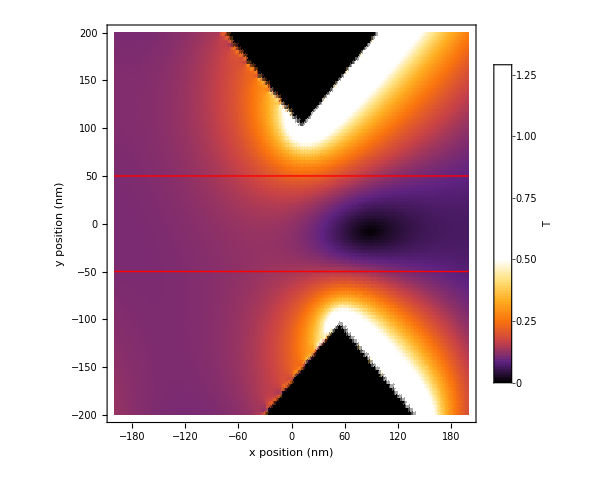

```mathematica
l1=Line[{{{-400*10^-0/2,-100*10^-0/2},{400*10^-0/2,-100*10^-0/2}},{{-400*10^-0/2,100*10^-0/2},{400*10^-0/2,100*10^-0/2}}}];

BmagPlot=ListDensityPlot[Bmag,DataRange->{{-xDistance/2,xDistance/2},{-yDistance/2,yDistance/2}},ClippingStyle->Blue,PlotLegends->BarLegend[Automatic,LegendLabel->"T"],PlotRange->{Min[Bmag],Max[Bmag]},(*PlotLabel->StringJoin[{"Bx-",PlotLabelName}],*)LabelStyle->{FontFamily->"Helvetica",24,GrayLevel[0]},ImageSize->500,(*Frame->True,*)FrameLabel->{{HoldForm["y position (nm)"],None},{HoldForm["x position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Small]],ColorFunction->(ColorData["SunsetColors"][Rescale[#,{Min[Bmag],0.5(*Max[Bmag]*)}]]&),ColorFunctionScaling->False];

aroundWirePlot=Show[{BmagPlot,Graphics[{Red,Thick,l1}]},PlotRange->All]

Export[StringJoin[{"Mathematica_out/",fileInfo,"/",fileInfo,"aroundWirePlot.eps"}],aroundWirePlot,"eps"];
```

```mathematica
(*This section is to plot z-slices of Bx,By,Bz and Bmag with a top down view on the system*)

inputfile=ImportString["..\\MuMax3\\Single Wire - Dragonfly\\HeatMap_InsideWire\\SingleWire_NoHysteresis_HeatMap.out\\B_eff.region40000000_fixed.mx"];
FieldData=Import[inputfile];

(*inputfile=ImportString["C:\\Program Files\\mumax3.9.1_windows\\RunFiles\\Catalouge of Data\\No Hysteresis\\SingleWire_NoHysteresis_HeatMap.out\\B_eff.region40000000.csv"];*)(*Full range*)(*inputfile=ImportString["C:\\Program Files\\mumax3.9.1_windows\\RunFiles\\SingleWire_NoHysteresis_HeatMap.out\\B_eff.region40000000.csv"];*)(*inputfile=ImportString["C:\\Program Files\\mumax3.9.1_windows\\RunFiles\\SingleWire_NoHysteresis_HeatMap.out\\B_eff000000.csv"];FieldData=Import[inputfile,"Data"];*)
(*FilePrint[inputfile]*)(*Prints out data*)
fileInfo="HeatMapSingleDragonFly";


SetDirectory[NotebookDirectory[]];
(*Setting where plots are created to current folder where this file is (or telling path to start from here)*)
CreateDirectory[StringJoin[{"Mathematica_out/",fileInfo,"/"}]];


(*Number of points for each direction,found in the batch file*)
(*Nz is the number of layers the data is given out for*)
Nx=400;
Ny=400;
Nz=16;

zlayer=7;(*Which z layer (given in Nz) I am chosing,it is a z slice I am plotting.FIRST SLICE IS 0*)numZerosStart=0;
numZerosEnd=0;(*Number of rows of 0 that appear at end of chunks of data in excel*)TopRowStart=numZerosStart+zlayer*Ny+zlayer+1 (*Row to start ON.Needs the 1 to start on row 1,the row end doesnt*)
TopRowEnd=Ny-numZerosEnd+zlayer*Ny+zlayer

TopRowStarty=numZerosStart+zlayer*Ny+zlayer+(Nz+1+Nz*Ny)
TopRowEndy=Ny-numZerosEnd+zlayer*Ny+zlayer+(Nz+Nz*Ny)

TopRowStartz=numZerosStart+zlayer*Ny+zlayer+2*(Nz+Nz*Ny)+1
TopRowEndz=Ny-numZerosEnd+zlayer*Ny+zlayer+2*(Nz+Nz*Ny)


Bx=FieldData[[TopRowStart;;TopRowEnd,1;;Nx]];
By=FieldData[[TopRowStarty;;TopRowEndy,1;;Nx]];
Bz=FieldData[[TopRowStartz;;TopRowEndz,1;;Nx]];
BxNan=Bx/.x_/;x==0->3*Max[Bx];
ByNan=By/.x_/;x==0->3*Max[By];
BzNan=Bz/.x_/;x==0->3*Max[Bz];
(*BxNan=Bx/.x_/;x==0->NaN;*)

Bmag=Sqrt[Bx^2+By^2+Bz^2];

(*xDistance=heatMapData[[lengthOfData,11]]*10^9;(*Taking max of x distance covered and finding range*)yDistance=heatMapData[[lengthOfData,12]]*10^9;(*Only records y at end of regions*)*)

xDistance=1800;(*Taking max of x distance covered and finding range*)yDistance=2400;(*Only records y at end of regions*)BxPlot=ListDensityPlot[BxNan,DataRange->{{-xDistance/2,xDistance/2},{-yDistance/2,yDistance/2}},ClippingStyle->Blue,PlotLegends->BarLegend[Automatic,LegendLabel->"T"],PlotRange->{Min[Bx],Max[Bx]},(*PlotLabel->StringJoin[{"Bx-",PlotLabelName}],*)LabelStyle->{FontFamily->"Helvetica",20,GrayLevel[0]},ImageSize->500,Frame->True,FrameLabel->{{HoldForm["y position (nm)"],None},{HoldForm["x position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Small]]]

ByPlot=ListDensityPlot[ByNan,DataRange->{{-xDistance/2,xDistance/2},{-yDistance/2,yDistance/2}},ClippingStyle->Blue,PlotLegends->BarLegend[Automatic,LegendLabel->"T"],PlotRange->{Min[By],Max[By]},(*PlotLabel->StringJoin[{"Bx-",PlotLabelName}],*)LabelStyle->{FontFamily->"Helvetica",20,GrayLevel[0]},ImageSize->500,Frame->True,FrameLabel->{{HoldForm["y position (nm)"],None},{HoldForm["x position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Small]]]

BzPlot=ListDensityPlot[BzNan,DataRange->{{-xDistance/2,xDistance/2},{-yDistance/2,yDistance/2}},ClippingStyle->Blue,PlotLegends->BarLegend[Automatic,LegendLabel->"T"],PlotRange->{Min[Bz],Max[Bz]},(*PlotLabel->StringJoin[{"Bx-",PlotLabelName}],*)LabelStyle->{FontFamily->"Helvetica",20,GrayLevel[0]},ImageSize->500,Frame->True,FrameLabel->{{HoldForm["y position (nm)"],None},{HoldForm["x position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Small]]]

(*BmagPlot=ListDensityPlot[Bmag,DataRange->{{-xDistance/2,xDistance/2},{-yDistance/2,yDistance/2}},ClippingStyle->Blue,PlotLegends->BarLegend[Automatic,LegendLabel->"T"],PlotRange->{Min[Bmag],Max[Bmag]},(*PlotLabel->StringJoin[{"Bx-",PlotLabelName}],*)LabelStyle->{FontFamily->"Helvetica",20,GrayLevel[0]},ImageSize->500,Frame->True,FrameLabel->{{HoldForm["y position (nm)"],None},{HoldForm["x position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Small]]]*)

BmagPlot=ListDensityPlot[Bmag,DataRange->{{-xDistance/2,xDistance/2},{-yDistance/2,yDistance/2}},ClippingStyle->Blue,PlotLegends->BarLegend[Automatic,LegendLabel->"T"],PlotRange->{Min[Bmag],Max[Bmag]},(*PlotLabel->StringJoin[{"Bx-",PlotLabelName}],*)LabelStyle->{FontFamily->"Helvetica",24,GrayLevel[0]},ImageSize->500,(*Frame->True,*)FrameLabel->{{HoldForm["y position (nm)"],None},{HoldForm["x position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Small]]]


Dimensions[Bz];
Dimensions[FieldData];
```

CreateDirectory::filex: C:\Users\Frolov Labuser\Documents\MalcolmJ\MicroMagneticPaperGitHub\Mathematica\Mathematica_out\HeatMapSingleDragonFly\ already exists.

2808

3207

9224

9623

15640

16039

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
(*This section is to make nice plot for just Bmag with view looking down*)Bmag=Sqrt[Bx^2+By^2+Bz^2];
BmagNan=Bmag/.x_/;x==0->3*Max[Bmag];
BmagPlot=ListDensityPlot[BmagNan,DataRange->{{-xDistance/2,xDistance/2},{-yDistance/2,yDistance/2}},ClippingStyle->RGBColor[120/255,120/255,120/255],PlotLegends->BarLegend[Automatic,LegendLabel->"T"],PlotRange->{Min[Bmag],Max[Bmag]},(*PlotLabel->StringJoin[{"Bx-",PlotLabelName}],*)LabelStyle->{FontFamily->"Helvetica",24,GrayLevel[0]},ImageSize->500,(*Frame->True,*)FrameLabel->{{HoldForm["y position (nm)"],None},{HoldForm["x position (nm)"],None}}(*,FrameStyle->Directive[Black,Thickness[Small]]*),ColorFunction->"SunsetColors"]

Export[StringJoin[{"Mathematica_out/",fileInfo,"/","Bmag_SingleMagnetX230Y1000Z100_slice50nm.eps"}],BmagPlot];
Export[StringJoin[{"Mathematica_out/",fileInfo,"/","Bmag_SingleMagnetX230Y1000Z100_slice50nm.png"}],BmagPlot];
```

-Graphics-